Finite element models of elasto-plastic materials
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 13 December 2021 - Contact: m.marino@ing.uniroma2.it

# Elements

## Q1EPS - Elasto-plasticity (small strain)

#### Initialization

```mathematica
<<AceGen`;

SMSInitialize["Q1EPS","Environment"-> "AceFEM","Mode"-> "Optimal"];

SMSTemplate["SMSTopology"->"Q1",
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson", "σYO -yield", "H -Hardening"},
 "SMSDefaultData" -> {100,0.49,1,10},

(*Time history element data*)
"SMSNoTimeStorage"-> lhg es$$["id","NoIntPoints"],
"SMSPostIterationCall"->True,

(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True
];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(*Number of element hystory variables*)
nhg =5; 
lhg=nhg+1;
)
```

#### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν,σYO,H}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
Ξn⊨{{-1,-1},{1,-1},{1,1},{-1,1}};
ℕh⊨Table[1/4(1+ξ Ξn⟦i,1⟧)(1+η Ξn⟦i,2⟧),{i,1,nen}];

(*ISOPARAMETRIC MAPPING*)
𝕏⊢SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];

ϵ=SMSVariables[𝔻];
GaussPointComputation[Ig];
Ψe⊨ElastoPlastic["EN",𝕙g];
)

ElastoPlastic[task_,𝕙g_]:=(
(*History variables*)
𝔻p={{𝕙g⟦1⟧,𝕙g⟦3⟧},{𝕙g⟦3⟧,𝕙g⟦2⟧}};
α⊢SMSFreeze[𝕙g⟦4⟧];
λ=𝕙g⟦5⟧;

(*Pseudo-energy*)
SMSFreeze[𝔻e,𝔻-𝔻p,"Symmetric"->True];
{λe,μe}⊢SMSHookeToLame[Ee,ν];
Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 H α^2;
If[task=="EN", Return[Ψe]];

(*Static quantities*)
SMSFreeze[σ,SMSD[Ψe,𝔻e,
		"Symmetric"->True],
			"Symmetric"->True];
SMSFreeze[q,-SMSD[Ψe,α]];

(*Yield function*)
σdev=σ-1/3 IdentityMatrix[ndim]Tr[σ];
fg⊨SMSSqrt[3/2 Tr[σdev.σdev]]-(σYO-q);
If[task=="f", Return[fg]];

(*Flow rule*)
𝕟σ=SMSD[fg,σ,"Symmetric"->True];
𝕟q=SMSD[fg,q];
𝔻pn={{𝕙gnIO⟦1⟧,𝕙gnIO⟦3⟧},
{𝕙gnIO⟦3⟧,𝕙gnIO⟦2⟧}};
αn=𝕙gnIO⟦4⟧;
λn=𝕙gnIO⟦5⟧;
ℚϵ=𝔻p-𝔻pn-(λ-λn)𝕟σ;
Qq=α-αn-(λ-λn)𝕟q;
Qλ=fg;
ℚ={ℚϵ⟦1,1⟧,ℚϵ⟦2,2⟧,ℚϵ⟦1,2⟧,Qq,Qλ};
If[task=="Q", Return[ℚ]];
)

GaussPointComputation[Ig_]:=(
Ihg⊢SMSInteger[(Ig-1)lhg];
(*Algorithm parameters*)
tol⊢SMSReal[rdata$$["SubIterationTolerance"]];
iNR⊢SMSInteger[idata$$["Iteration"]];
(*Previous time step*)
𝕙gnIO⊢SMSIO["Element time dependent data n"[Table[Ihg+i,{i,nhg}]]];
staten⊢SMSIO["Element time dependent data n"[Ihg+nhg+1]];
(*Initialize trial: plastic variables are freezed*)
ftr⊨ElastoPlastic["f",𝕙gnIO];

SMSIf[(iNR==1 && staten==0)||(iNR>1 && ftr<tol)];
	(*Elastic step*)
	𝕙g⫤𝕙gnIO;
	SMSIO[Join[𝕙g,{0}],"Export to",
			"Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
SMSElse[];
	(*Plastic step*)
	𝕙gb⫤𝕙gnIO;
	SMSDo[jNR,1,30,1,𝕙gb];
		ℚg⊨ElastoPlastic["Q",𝕙gb];
		𝔸g⊨SMSD[ℚg,𝕙gb];
		Δ𝕙⊨SMSLinearSolve[𝔸g,-ℚg];
		𝕙gb⊣𝕙gb+Δ𝕙;
		
		SMSIf[SMSSqrt[Δ𝕙.Δ𝕙]<tol];
			SMSIO[Join[𝕙gb,{1}], "Export to", 
				  "Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
			D𝕙Dϵ⫤SMSLinearSolve[𝔸g,-SMSD[ℚg,ϵ,"Constant"->𝕙gb]];
			SMSBreak[];
		SMSEndIf[D𝕙Dϵ];
		
		SMSIf[jNR=="29"];
		SMSExport[{1,2},{idata$$["SubDivergence"],idata$$["ErrorStatus"]}];
			SMSBreak[];
		SMSEndIf[];
	SMSEndDo[𝕙gb,D𝕙Dϵ];

	𝕙g⊣SMSFreeze[𝕙gb,"Dependency"->{ϵ,D𝕙Dϵ}];
SMSEndIf[𝕙g];
)
```

#### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i,"Constant"->𝕙g];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

#### Post - processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
𝔻p⊨𝔻-𝔻e;
σ⊨SMSD[Ψe,𝔻e,"Symmetric"->True];
σdev⊨σ-1/3 IdentityMatrix[ndim]Tr[σ];
σVM⊨SMSSqrt[3/2 Tr[σdev.σdev]];

SMSIO[
{"ϵxx"->𝔻⟦1,1⟧,"ϵxy"->𝔻⟦1,2⟧,"ϵyy"->𝔻⟦2,2⟧,"ϵexx"->𝔻e⟦1,1⟧,"ϵexy"->𝔻e⟦1,2⟧,"ϵeyy"->𝔻e⟦2,2⟧,"ϵpxx"->𝔻p⟦1,1⟧,"ϵpxy"->𝔻p⟦1,2⟧,"ϵpyy"->𝔻p⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧,"σVM"-> σVM,"α"->α,"λ"->λ,"Ψe"->Ψe}
,"Export to","Integration point post"[Ig]];

SMSEndDo[];

𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
```

#### Code generation

```mathematica
SMSWrite[];
{{"File: ""Q1EPS.c""  Size: "20949"  Time: "8}, {{{"Method", "SKR", "SPP"}, {"No.Formulae", 246, 185}, {"No.Leafs", 3340, 2548}}}}
```

## Q1EPS-2

### Initialization

```mathematica
<<AceGen`;

SMSInitialize["Q1EPS2","Environment"-> "AceFEM","Mode"-> "Optimal"];

SMSTemplate["SMSTopology"->"Q1",
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson", "σYO -yield", "H -Hardening"},
 "SMSDefaultData" -> {100,0.49,1,10},

(*Time history element data*)
"SMSNoTimeStorage"-> lhg es$$["id","NoIntPoints"],
"SMSPostIterationCall"->True,

(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True
];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(*Number of element hystory variables*)
nhg =7; 
lhg=nhg+1;
)
```

### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν,σYO,H}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
Ξn⊨{{-1,-1},{1,-1},{1,1},{-1,1}};
ℕh⊨Table[1/4(1+ξ Ξn⟦i,1⟧)(1+η Ξn⟦i,2⟧),{i,1,nen}];

(*ISOPARAMETRIC MAPPING*)
𝕏⊢SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];

ϵ=SMSVariables[𝔻];
GaussPointComputation[Ig];
Ψe⊨ElastoPlastic["EN",𝕙g];
)

ElastoPlastic[task_,𝕙g_]:=(
(*History variables*)
𝔻p={{𝕙g⟦1⟧,𝕙g⟦3⟧},{𝕙g⟦3⟧,𝕙g⟦2⟧}};
(*α⊢SMSFreeze[𝕙g⟦4⟧];*)
SMSFreeze[α,{{𝕙g⟦4⟧,𝕙g⟦6⟧},{𝕙g⟦6⟧,𝕙g⟦5⟧}},"Symmetric"->True];
(*λ=𝕙g⟦5⟧;*)
λ=𝕙g⟦7⟧;

(*Pseudo-energy*)
SMSFreeze[𝔻e,𝔻-𝔻p,"Symmetric"->True];
{λe,μe}⊢SMSHookeToLame[Ee,ν];
(*Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 H α^2;*)
(*Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 Transpose[α]H α;*)
Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 H Tr[Transpose[α].α];
If[task=="EN", Return[Ψe]];

(*Static quantities*)
SMSFreeze[σ,SMSD[Ψe,𝔻e,
		"Symmetric"->True],
			"Symmetric"->True];
SMSFreeze[q,-SMSD[Ψe,α,"Symmetric"->True],"Symmetric"->True];

(*Yield function*)
σdev=σ-1/3 IdentityMatrix[ndim] Tr[σ];
(*fg⊨SMSSqrt[3/2 Tr[σdev.σdev]]-(σYO-q);*)
(*fg⊨SMSSqrt[3/2 Norm[σdev-q]]-(σYO);(* LA RADICE ?????*)*)
fg⊨SMSSqrt[3/2 Tr[Transpose[σdev-q].(σdev-q)]]-(σYO);
If[task=="f", Return[fg]];

(*Flow rule*)
𝕟σ=SMSD[fg,σ,"Symmetric"->True];
𝕟q=SMSD[fg,q,"Symmetric"->True];
𝔻pn={{𝕙gnIO⟦1⟧,𝕙gnIO⟦3⟧},
{𝕙gnIO⟦3⟧,𝕙gnIO⟦2⟧}};
(*αn=𝕙gnIO⟦4⟧;*)
αn={{𝕙gnIO⟦4⟧,𝕙gnIO⟦6⟧},
{𝕙gnIO⟦6⟧,𝕙gnIO⟦5⟧}};
λn=𝕙gnIO⟦7⟧;
ℚϵ=𝔻p-𝔻pn-(λ-λn)𝕟σ;
Qq=α-αn-(λ-λn)𝕟q;
Qλ=fg;
ℚ={ℚϵ⟦1,1⟧,ℚϵ⟦2,2⟧,ℚϵ⟦1,2⟧,Qq⟦1,1⟧,Qq⟦2,2⟧,Qq⟦1,2⟧,Qλ};
If[task=="Q", Return[ℚ]];
)

GaussPointComputation[Ig_]:=(
Ihg⊢SMSInteger[(Ig-1)lhg];
(*Algorithm parameters*)
tol⊢SMSReal[rdata$$["SubIterationTolerance"]];
iNR⊢SMSInteger[idata$$["Iteration"]];
(*Previous time step*)
𝕙gnIO⊢SMSIO["Element time dependent data n"[Table[Ihg+i,{i,nhg}]]];
staten⊢SMSIO["Element time dependent data n"[Ihg+nhg+1]];
(*Initialize trial: plastic variables are freezed*)
ftr⊨ElastoPlastic["f",𝕙gnIO];

SMSIf[(iNR==1 && staten==0)||(iNR>1 && ftr<tol)];
	(*Elastic step*)
	𝕙g⫤𝕙gnIO;
	SMSIO[Join[𝕙g,{0}],"Export to",
			"Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
SMSElse[];
	(*Plastic step*)
	𝕙gb⫤𝕙gnIO;
	SMSDo[jNR,1,30,1,𝕙gb];
		ℚg⊨ElastoPlastic["Q",𝕙gb];
		𝔸g⊨SMSD[ℚg,𝕙gb];
		Δ𝕙⊨SMSLinearSolve[𝔸g,-ℚg];
		𝕙gb⊣𝕙gb+Δ𝕙;
		
		SMSIf[SMSSqrt[Δ𝕙.Δ𝕙]<tol];
			SMSIO[Join[𝕙gb,{1}], "Export to", 
				  "Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
			D𝕙Dϵ⫤SMSLinearSolve[𝔸g,-SMSD[ℚg,ϵ,"Constant"->𝕙gb]];
			SMSBreak[];
		SMSEndIf[D𝕙Dϵ];
		
		SMSIf[jNR=="29"];
		SMSExport[{1,2},{idata$$["SubDivergence"],idata$$["ErrorStatus"]}];
			SMSBreak[];
		SMSEndIf[];
	SMSEndDo[𝕙gb,D𝕙Dϵ];

	𝕙g⊣SMSFreeze[𝕙gb,"Dependency"->{ϵ,D𝕙Dϵ}];
SMSEndIf[𝕙g];
)
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i,"Constant"->𝕙g];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
𝔻p⊨𝔻-𝔻e;
σ⊨SMSD[Ψe,𝔻e,"Symmetric"->True];
σdev⊨σ-1/3 IdentityMatrix[ndim]Tr[σ];
σVM⊨SMSSqrt[3/2 Tr[σdev.σdev]];

SMSIO[
{"ϵxx"->𝔻⟦1,1⟧,"ϵxy"->𝔻⟦1,2⟧,"ϵyy"->𝔻⟦2,2⟧,"ϵexx"->𝔻e⟦1,1⟧,"ϵexy"->𝔻e⟦1,2⟧,"ϵeyy"->𝔻e⟦2,2⟧,"ϵpxx"->𝔻p⟦1,1⟧,"ϵpxy"->𝔻p⟦1,2⟧,"ϵpyy"->𝔻p⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧,"σVM"-> σVM,"α"->α,"λ"->λ,"Ψe"->Ψe}
,"Export to","Integration point post"[Ig]];

SMSEndDo[];

𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
```

### Code generation

```mathematica
SMSWrite[];
```

File: Q1EPS2.c  Size: 29542  Time: 16
Method | SKR | SPP
No.Formulae | 338 | 268
No.Leafs | 5250 | 4108

# FEM Simulations

## Patch test

### Definition of Mesh, Loads and Boundary Conditions

```mathematica
myPatch[element_,OptionsPattern[]]:=(
L=1;
ϵmax=0.1;

<<AceFEM`;
SMTInputData[];
(*SMTAddDomain["Ωc","Q1EPS",{"E *"-> 100,"ν *"-> 0.3,"σYO *"->5,"H *"->10}];*)
SMTAddDomain["Ωc",element,{"E *"-> OptionValue["σYO"]/0.002,"ν *"-> 0.3,"σYO *"->OptionValue["σYO"],"H *"->OptionValue["H"]}];


SMTAddNode[L{{0.0,0.0},{0.0,1.0},{0.2,0.15},{0.75,0.3},{1.0,0.0},{0.25,0.7},{0.75,0.75},{1.0,1.0}}];
SMTAddElement[{{"Ωc",{1,5,4,3}},{"Ωc",{1,3,6,2}},{"Ωc",{2,6,7,8}},{"Ωc",{8,7,4,5}},{"Ωc",{7,6,3,4}}}];

SMTAddEssentialBoundary[Point[{0,0},"D"],1->0,2->0];
SMTAddEssentialBoundary[Point[{0,L},"D"],1->0,2->ϵmax L];
SMTAddEssentialBoundary[Point[{L,0},"D"],2->0];
SMTAddEssentialBoundary[Point[{L,L},"D"],2->ϵmax L];
SMTAnalysis[];
)
Options[myPatch]={"σYO"->5,"H"->10}
```

{σYO→5,H→10}

### Solution algorithm (loading-unloading, adaptive)

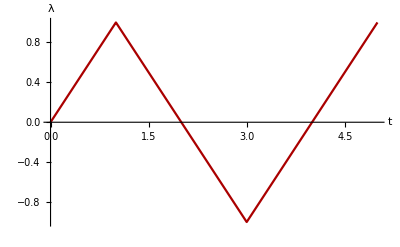

```mathematica
tMax=5;
λf[t_]:=If[OddQ[Floor[(t+1)/2]],1,-1] (2 Floor[(t+1)/2]-t);
Plot[λf[t],{t,0,tMax},AxesLabel->{"t","λ"},
PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

```mathematica
SolveMyPatch[]:=(
tMax=5;
λf[t_]:=If[OddQ[Floor[(t+1)/2]],1,-1] (2 Floor[(t+1)/2]-t);
Clear[σ]; σ={{0,0}};
t0=0.1;ΔtMin=0.0001;ΔtMax=0.1;
tolNR=10^-8;maxNR=50;targetNR=15;
SMTNextStep["t"->t0,"λ[t]"->λf];
While[ 
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive Time",targetNR,ΔtMin,ΔtMax,tMax}]
,SMTNewtonIteration[];];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];]; 
step⟦3⟧ ,If[step⟦1⟧
,SMTStepBack[];,
AppendTo[σ,{SMTPostData["ϵyy",{L/2,L/2}],SMTPostData["σyy",{L/2,L/2}]}];
];
SMTNextStep["Δt"->step⟦2⟧,"λ[t]"->λf];];
AppendTo[σ,{SMTPostData["ϵyy",{L/2,L/2}],SMTPostData["σyy",{L/2,L/2}]}];
Return[σ];
)
```

### Results

```mathematica
<<AceFEM`
```

σyo=175, H=11600/11

-Graphics-

σyo=200, H=11600/11

-Graphics-

σyo=225, H=11600/11

-Graphics-

σyo=250, H=11600/11

-Graphics-

σyo=275, H=11600/11

-Graphics-

σyo=300, H=11600/11

-Graphics-

σyo=325, H=11600/11

-Graphics-

σyo=350, H=11600/11

-Graphics-

σyo=375, H=11600/11

-Graphics-

σyo=400, H=11600/11

-Graphics-

σyo=425, H=11600/11

-Graphics-

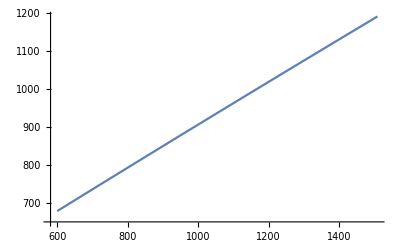

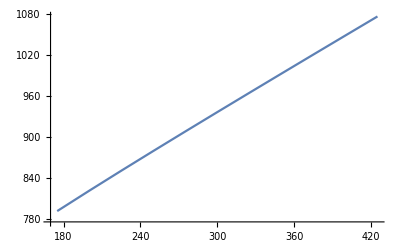

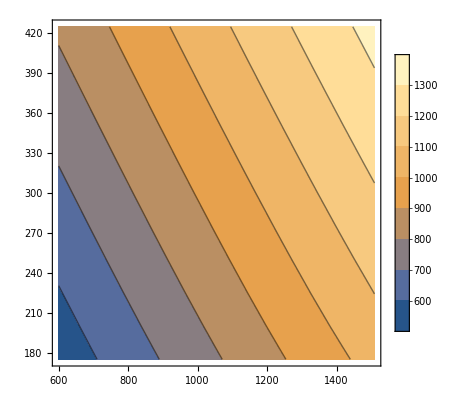

```mathematica
Npassi=11;
harden=Table[600+i((1600-600)/Npassi),{i,0,Npassi-1}];
σyo=Table[175+i((450-175)/Npassi),{i,0,Npassi-1}];
myσ=Table[{0i,0j},{i,1,Length[harden]},{j,1,Length[σyo]}];
Do[Do[
myPatch["Q1EPS","σYO"->σyo⟦j⟧,"H"->harden⟦i⟧];
σ=SolveMyPatch[];
myσ⟦i,j⟧=Max[σ];
If[i==(Length[myσ]+1)/2,
Print["σyo=",σyo⟦j⟧,", H=",harden⟦i⟧];
Print[ListLinePlot[σ,AxesLabel->{"ϵyy","σyy"},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]]]
,{i,1,Length[harden]}],{j,1,Length[σyo]}]
ListLinePlot[Table[{harden⟦i⟧,myσ⟦i,(Length[myσ]+1)/2⟧},{i,1,Length[myσ]}]]
ListLinePlot[Table[{σyo⟦i⟧,myσ⟦(Length[myσ]+1)/2,i⟧},{i,1,Length[myσ]}]]
list=Flatten[Table[{harden⟦i⟧,σyo⟦j⟧,myσ⟦i,j⟧},{i,1,Length[myσ]},{j,1,Length[myσ]}],1];
ListContourPlot[list,PlotLegends->Automatic]
```

```mathematica
ListLinePlot[σ,AxesLabel->{"ϵyy","σyy"},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

{{0,0},{0.01,404.611},{0.02,419.694},{0.03,434.778},{0.04,449.861},{0.05,464.945},{0.06,480.029},{0.07,495.112},{0.08,510.196},{0.09,525.279},{0.1,540.363},{0.09,-547.167},{0.08,-562.25},{0.07,-577.334},{0.06,-592.418},{0.05,-607.501},{0.04,-622.585},{0.03,-637.668},{0.02,-652.752},{0.01,-667.835},{-4.57786×10^-17,-682.919},{-0.01,-698.002},{-0.02,-713.086},{-0.03,-728.169},{-0.04,-743.253},{-0.05,-758.337},{-0.06,-773.42},{-0.07,-788.504},{-0.08,-803.587},{-0.09,-818.671},{-0.1,-833.754},{-0.09,836.063},{-0.08,851.147},{-0.07,866.23},{-0.06,881.314},{-0.05,896.397},{-0.04,911.481},{-0.03,926.564},{-0.02,941.648},{-0.01,956.731},{1.79815×10^-16,971.815},{0.01,986.899},{0.02,1001.98},{0.03,1017.07},{0.04,1032.15},{0.05,1047.23},{0.06,1062.32},{0.07,1077.4},{0.08,1092.48},{0.09,1107.57},{0.1,1122.65}}

1122.65

-Graphics-

```mathematica
Show[SMTShowMesh["Field"->"ϵyy","DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,ImageSize->300]]
```

-Graphics-

## Plate with crack

### Definition of Mesh, Loads and Boundary Conditions

```mathematica
DomainDefinition[element_,crack_,load_,OptionsPattern[]]:=(
L=10; H=L; 
a=crack;
points1={{0,0},{L,0},{L,H/2},{0,H/2}};
points2={{0,H/2},{L,H/2},{L,H},{0,H}};
densmesh=100;
<<AceFEM`;
SMTInputData[];
SMTAddDomain[
{"Ωc1",element,{"E *"-> OptionValue["σYO"]/0.002,"ν *"-> 0.3,"σYO *"->OptionValue["σYO"],"H *"->OptionValue["H"]}}
,
{"Ωc2",element,{"E *"-> OptionValue["σYO"]/0.002,"ν *"-> 0.3,"σYO *"->OptionValue["σYO"],"H *"->OptionValue["H"]}}
];
SMTAddMesh[Polygon[points1],"Ωc1","Q1",{densmesh,densmesh/2}];
SMTAddMesh[Polygon[points2],"Ωc2","Q1",{densmesh,densmesh/2}];

(*q=300;*)
q=load;
SMTAddEssentialBoundary[{Line[{{0,0},{L,0}},"D"],2-> 0}];
SMTAddEssentialBoundary[{Line[{{0,0},{0,H}},"D"],1-> 0}];
SMTAddNaturalBoundary[Line[{{0,H},{L,H}},"D"],2->Line[{q}]];
SMTAnalysis["Tie"->{True,("Y"== H/2 && "X" <a &)}];

)
Options[DomainDefinition]={"σYO"->5,"H"->10};
```

### Solution algorithm (adaptive load-step, NR loop) - WITH POSTPROCESSING

```mathematica
solveSimulation[OptionsPattern[]]:=(
tolNR=10^-8;maxNR=50;targetNR=8;
λMax=1;λ0=λMax/20;ΔλMin=λMax/100;ΔλMax=λMax/20;
qv={{0,0}};
SMTNextStep["λ"->λ0];
While[
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive BC",targetNR,ΔλMin,ΔλMax,λMax}]
, SMTNewtonIteration[];
];
If[OptionValue["animation"],
If[Not[step⟦1⟧],SMTAnimationOfResponse["x"-> Hold[SMTData["Multiplier"]] ,"y"->Hold[Total[ SMTPostData["v",Point[{0,0.1 H +(H/2)}]]]],"LeadingNodePosition"->{0,H},"ImageSize"->600,"Show"->"Window"|{"ExportFrames","responseFile"}]
]
];

If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];];
step⟦3⟧ 
,If[step⟦1⟧(*True if NOT converged*),
SMTStepBack[];
, (*Postprocessing*)
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{0,0.1 H+(H/2)}]]}];
];
SMTNextStep["Δλ"->step⟦2⟧]
];
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{0,0.1 H+(H/2)}]]}];
(*SMTAnimationOfResponse["Animate"]*)
If[OptionValue["ExportAnimation"],
SMTAnimationOfResponse["Export to","mp4","FirstFrame"->"LastFrame"]
]
)
Options[solveSimulation]={"animation"->True,"ExportAnimation"->False};
```

```mathematica
(*SMTAnimationOfResponse["Export to","mp4","FirstFrame"->"LastFrame"]*)
```

responseFile.mp4

### Results

```mathematica
Show[SMTShowMesh["DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,"BoundaryConditions"->True,ImageSize->300]]
```

-Graphics-

```mathematica
ListLinePlot[qv,AxesLabel->{"λq","v"},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

-Graphics-

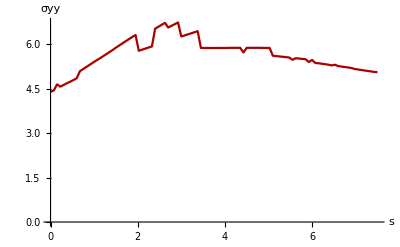

```mathematica
nx=100;
S=L-a;
σy=Table[
{S(i-1)/nx,
SMTPostData["σyy",Point[{S(i-1)/nx+a,H/2}]]},
{i,1,nx+1}];
ListLinePlot[σy,AxesLabel->{"s","σyy"},PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,S},{0,All}}]
```

```mathematica
(*β=Sqrt[Sec[Pi a /L]]*)
β=Sqrt[(4L/(Pi a)) Tan[Pi a /(4 L)]];
(*σinf=σy⟦1,2⟧;*)
σinf=q;
Kfactor=β σinf Sqrt[Pi a];
Kfactor2=σinf*Sqrt[Pi a]*((1-(a/(2L))+0.326*(a/L)^2)/Sqrt[1-(a/L)]);
Print["Fattore di intensificazione degli sforzi teorico 1: ",N[Kfactor]]
Print["Fattore di intensificazione degli sforzi teorico 2: ",N[Kfactor2]]
(*Print["Rapporto: ",N[Kfactor/Sqrt[Pi a]]]*)
```

```mathematica
SMTPostData["v",Point[{0,H/2}]]
```

-0.198929

## Final plate

```mathematica
<<AceFEM`;
```

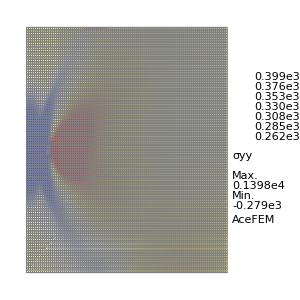
-Graphics--Graphics-

Lunghezza della cricca: 1/8

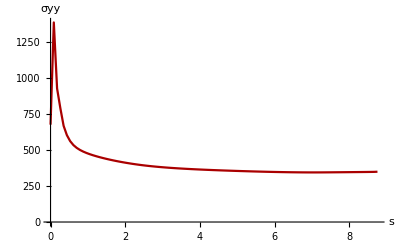

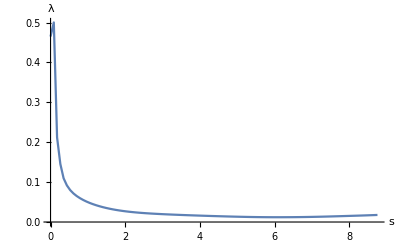

r_p: 6.0375

K: 9559.49

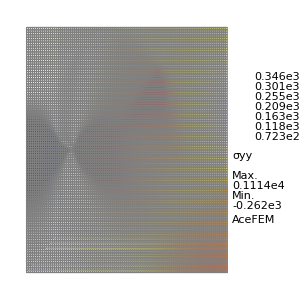
-Graphics--Graphics-

Lunghezza della cricca: 1/4

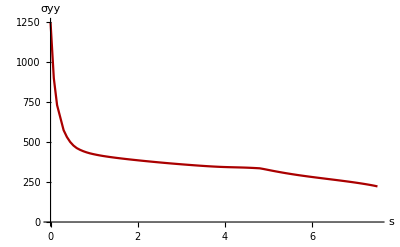

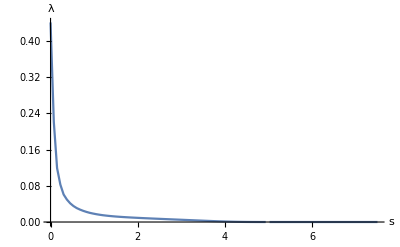

r_p: 4.95

K: 7776.57

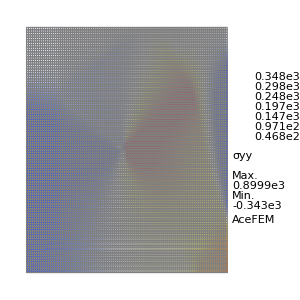
-Graphics--Graphics-

Lunghezza della cricca: 1/2

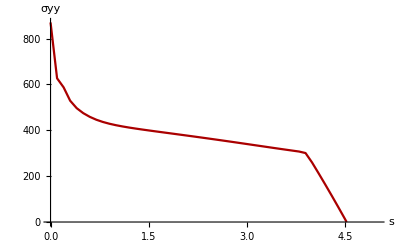

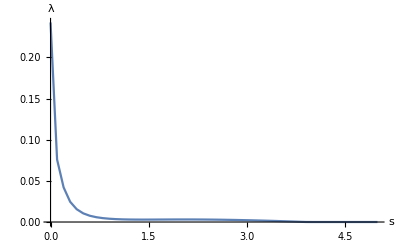

r_p: 4.

K: 4879.67

-Graphics--Graphics-

Lunghezza della cricca: 3/4

-Graphics-

-Graphics-

r_p: 2.5

K: 3946.59

```mathematica
Npassi=11;
harden=Table[600+i((1600-600)/Npassi),{i,0,Npassi-1}];
σyo=Table[175+i((450-175)/Npassi),{i,0,Npassi-1}];
crack={L/8, L/4,L/2,3L/4};
nx=100;
σy=Table[i*0,{i,1,Length[crack]}];
σyMAX=Table[i*0,{i,1,Length[crack]}];
Dy=Table[i*0,{i,1,Length[crack]}];
load={350,270,160,85};
ν=0.3;
lambda=Table[i*0,{i,1,Length[crack]}];
xLambda=Table[i*0,{i,1,Length[crack]}];
zeroVal=Table[i*0,{i,1,Length[crack]}];
K=Table[i*0,{i,1,Length[crack]}];
rp=Table[i*0,{i,1,Length[crack]}];
Do[
DomainDefinition["Q1EPS",crack⟦j⟧,load⟦j⟧,"σYO"->Mean[σyo],"H"->Mean[harden]];
solveSimulation["animation"->False,"ExportAnimation"->False];
Print[Show[SMTShowMesh["DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,"BoundaryConditions"->True,ImageSize->300]],Show[SMTShowMesh["DeformedMesh"->False,"Field"->"σyy",ImageSize->300]]];
S=L-crack⟦j⟧;
σy=Table[{S(i-1)/nx,SMTPostData["σyy",Point[{S(i-1)/nx+crack⟦j⟧,H/2}]]},{i,1,nx+1}];
σyMAX⟦j⟧=Max[Transpose[σy]⟦2⟧];
Print["Lunghezza della cricca: ",crack[[j]]/L];
Print[ListLinePlot[σy,AxesLabel->{"s","σyy"},PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,All},{0,All}}]];
Dy⟦j⟧=Table[{S(i-1)/nx,SMTPostData["λ",Point[{S(i-1)/nx+crack⟦j⟧,H/2}]]},{i,1,nx+1}];
Print[ListLinePlot[Dy⟦j⟧,AxesLabel->{"s","λ"},LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,S},{0,All}}]];

lambda⟦j⟧=Table[Dy⟦j,i,2⟧,{i,1,Length[Dy⟦j⟧]}];
xLambda⟦j⟧=Table[Dy⟦j,i,1⟧,{i,1,Length[Dy⟦j⟧]}];
(*Print[ListLinePlot[Dy⟦1⟧,AxesLabel->{"s","λ"},LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,All},{0,All}}]]*)
(*Print[ListLinePlot[Transpose[{xLambda⟦j⟧,lambda⟦j⟧}],AxesLabel->{"s","λ"},LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,All},{0,All}}]];*)
zeroVal⟦j⟧=Min[lambda⟦j⟧];
(*If[zeroVal⟦j⟧!=0,
lambda⟦j⟧=lambda⟦j⟧-zeroVal⟦j⟧;
];*)
(*Position[lambda1,0.]*)
rp⟦j⟧=Extract[xLambda⟦j⟧,Position[lambda⟦j⟧,zeroVal⟦j⟧]⟦1⟧];
Print[Subscript["r","p"],": ",N[rp⟦j⟧]];
K⟦j⟧=Sqrt[(N[rp⟦j⟧] Pi (σyMAX⟦j⟧)^2) / (1-2ν)];
Print["K: ",K⟦j⟧];
,{j,1,Length[crack]}]
```

```mathematica
(*lambda1=Table[Dy⟦1,i,2⟧,{i,1,Length[Dy⟦1⟧]}];
x1=Table[Dy⟦1,i,1⟧,{i,1,Length[Dy⟦1⟧]}];
(*Print[ListLinePlot[Dy⟦1⟧,AxesLabel->{"s","λ"},LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,All},{0,All}}]]*)
lambda1=lambda1-Min[lambda1];
Print[ListLinePlot[Transpose[{x1,lambda1}],AxesLabel->{"s","λ"},LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,All},{0,All}}]]

Position[lambda1,0.]
rp=Extract[x1,Position[lambda1,0.]]
ν=0.3;
σyMAX⟦1⟧;
K=Sqrt[N[rp] Pi σyMAX⟦1⟧^2 / (1-2ν)]*)
```

```mathematica
Flatten[K]
```

{10098.5,7537.23,4693.12,3348.79}

```mathematica
ListPlot[Transpose[{N[crack/L],Flatten[K]}],PlotRange->{{0,1},{0,All}},AxesLabel->{"a/L","K"},PlotMarkers->{"*",20},LabelingFunction->(NumberForm[#1⟦2⟧]&)]
```

-Graphics-

```mathematica
SMTAnimationOfResponse["Animate"]
```

5/4

```mathematica
nx=100;
S=L-a;
σy=Table[
{S(i-1)/nx,
SMTPostData["σyy",Point[{S(i-1)/nx+a,H/2}]]},
{i,1,nx+1}];
ListLinePlot[σy,AxesLabel->{"s","σyy"},PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,S},{0,All}}]
```

-Graphics-

```mathematica
ListLinePlot[qv,AxesLabel->{"λq",Subscript["v","H/2"]},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

-Graphics-